# Tree-level graviton scattering with FeynArts

Tree-level four-graviton scattering with FeynArts. The notebook works in three stages and gives every intermediate result a name, so any cell can be re-evaluated on its own.

First it builds the complete 2 → 2 tree amplitude off shell. FeynArts generates the three exchange diagrams and the four-graviton contact, the external polarisation tensors are attached as formal factorised tensors, and each diagram is contracted with FORM. The total is stored in theAmplitude[p1, p2, p3, p4].

Then it imposes the massless on-shell kinematics: FCClearScalarProducts[] removes earlier scalar-product assignments, SetMandelstam fixes the momentum products p_i·p_j, and a block of Pair assignments fixes the polarisation contractions, namely transversality of each wavefunction, the null property ε_i·ε_i=0, and the polarisation-momentum and polarisation-polarisation tables.

Finally it reduces the result to helicity amplitudes labelled by h_1,h_2,h_3,h_4=±1 and compares four combinations with closed forms in s, t and u.

Conventions: metric signature (+, -, -, -); FeynArts treats all external momenta as incoming, so the physical outgoing momenta p3 and p4 enter SetMandelstam as -p3 and -p4 and their polarisations carry the conjugated label -I. The gauge parameter is fixed at 2 by the model. No loop integration, spin sum or cross section is computed.

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the two cells below with Shift+Enter. The first loads FeynGrav, which loads FeynCalc and CalcFormConverter, and asks FeynCalc to load the installed patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. GenericModel is given explicitly because the classes file does not name its generic model and the FeynArts default is the stock "Lorentz" file. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
grModel="PureGR";
InitializeModel[grModel,GenericModel->grModel];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

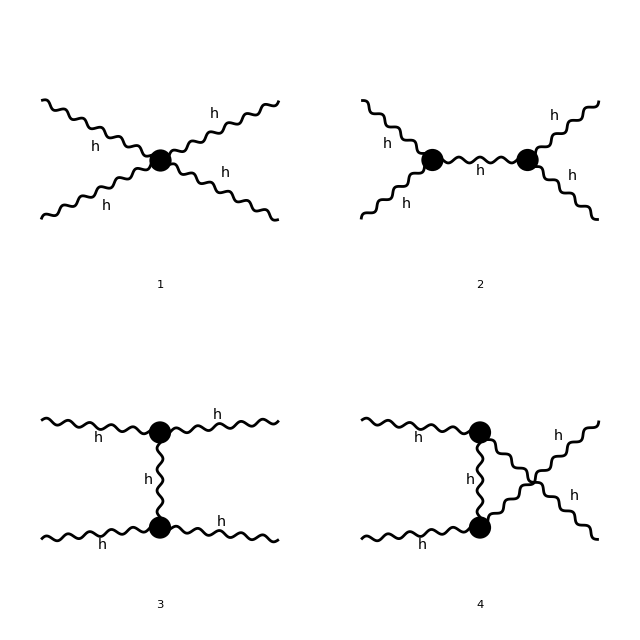

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 4. Form the total off-shell amplitude

Contract the diagrams separately with FORM to limit intermediate expression sizes. Each contraction uses CalcFormCalculate with its default options: the Lorentz dimension is inferred from the expression, which carries symbolic D, and successful FORM jobs are cleaned up automatically. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced.

The four contracted diagrams are summed immediately into theAmplitude[p1, p2, p3, p4]. The momenta are arguments of that definition, so a permuted evaluation, for instance the exchange of the two incoming legs, can be formed later from the same stored expression.

```mathematica
theAmplitude[p1_,p2_,p3_,p4_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;
```

theAmplitude[p1, p2, p3, p4] now holds the complete polarisation-contracted, amputated off-shell tree expression: all four diagrams with their graph factors, and still with unconstrained external virtualities, longitudinal contractions and trace terms.

Short shows only a preview and Length counts the terms of the stored expression; neither changes it. This is not yet an on-shell scattering amplitude, and it contains no loop measure or spin sum.

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D (p1·ε(p2)) (p2·ε(p1)) («1») (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

## 5. On-shell amplitude

Everything above is off shell: the p_i^2 and the polarisation contractions are still free. This section fixes them in three steps, clearing the old scalar products, fixing the momenta and fixing the polarisations, and then reduces the result to helicity amplitudes.

The Pair assignments below are global and persist for the session. To return to the off-shell expression, restart the kernel rather than trying to undo them cell by cell.

FCClearScalarProducts[] removes any scalar-product assignments made earlier in the session, so the on-shell relations that follow are applied to a clean state rather than on top of stale values.

```mathematica
FCClearScalarProducts[]
```

SetMandelstam fixes the momentum products p_i·p_j for massless momenta. The physical outgoing momenta p3 and p4 are passed as -p3 and -p4 because SetMandelstam works with all-incoming momenta, and the four mass arguments are zero. This sets p_1·p_2=p_3·p_4=s/2, p_1·p_3=p_2·p_4=-t/2, and p_1·p_4=p_2·p_3=-u/2, which implies s + t + u = 0 together with t=-2 E^2(1-cosθ) and u=-2E^2(1+cosθ) in the centre-of-mass frame. Nothing is said yet about the polarisations.

```mathematica
SetMandelstam[s, t, u, p1 , p2 , -p3 , -p4 , 0 , 0 , 0 , 0 ];
```

Transversality: each wavefunction is orthogonal to its own momentum, ε_i,p_i=0. The momentum is the physical one, so this holds for the incoming legs 1 and 2 and for the conjugated outgoing legs 3 and 4.

```mathematica
Pair[Momentum[p1,D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[p2,D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[p3,D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[p4,D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

Null wavefunctions: ε_i·ε_i=0 in the bilinear product. This is a statement about each leg on its own; the products between different legs are fixed by the two blocks that follow.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

The mixed products that vanish: ε_1·p_2, ε_2·p_1, ε_3·p_4, and ε_4·p_3 are zero. Each wavefunction has zero time component, so these reduce to spatial scalar products, which vanish for the leg pairings shown.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p2,D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p1,D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p4,D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p3,D]]=0;
```

The polarisation-momentum products. With h_i=±1 the whole block equals ⅈ √((t u)/(2 s)) times a matrix built from the helicity labels; it is written out leg by leg here. The products are bilinear, with no complex conjugation, and the momenta are the physical ones.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p3,D]]=-h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p4,D]]=h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p3,D]]=h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p4,D]]=-h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p1,D]]=-h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p2,D]]=h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p1,D]]=h4 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p2,D]]=-h4 ⅈ/Sqrt[2] Sqrt[t u/s];
```

The polarisation-polarisation products, again bilinear with no conjugation. The diagonal is zero because each wavefunction is null. Off the diagonal the entries carry the helicity labels of the two legs together with the ratio t/s; using 1+2 t/s=cosθ they encode the helicity correlations that the final amplitudes are built from.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=-(1+h1 h2)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=-(h1 h3 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=(h1 h4 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=(h2 h3 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(h2 h4 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(1+h3 h4)/2;
```

Simplify needs to know that the helicity labels are ±1 before it can collapse the polynomials in h_i introduced by the tables above.

```mathematica
$Assumptions=h1^2==h2^2==h3^2==h4^2==1;
```

This is where the off-shell expression becomes a helicity amplitude. theAmplitude already depends on s, t and u through the assignments above; Simplify applies the h_i^2=1 assumptions and TrickMandelstam rewrites the result in the standard variables, storing it in theAmplitudeonShell, again as a function of the four helicity labels.

```mathematica
theAmplitudeonShell[h1_,h2_,h3_,h4_]=TrickMandelstam[theAmplitude[p1,p2,p3,p4]//Simplify,{s,t,u,0}];//Timing
```

{1.43397,Null}

Check against closed forms. Each of the four helicity combinations is compared with the expected tree-level expression. Both sides are put in s, t and u by TrickMandelstam before the comparison. The recorded outputs are True for each combination.

```mathematica
TrickMandelstam[theAmplitudeonShell[+1,+1,+1,+1],{s,t,u,0}]==ⅈ κ^2/4 s^4/(s t u)
TrickMandelstam[theAmplitudeonShell[+1,-1,-1,+1],{s,t,u,0}]==ⅈ κ^2/4 t^4/(s t u)
TrickMandelstam[theAmplitudeonShell[+1,-1,+1,-1],{s,t,u,0}]==ⅈ κ^2/4 u^4/(s t u)
```

True

True

True

Scope of the result. This is the massless tree-level four-graviton amplitude, evaluated with the gauge parameter fixed at 2 by the model, using the polarisation conventions fixed above; h_i=±1 are the helicity labels. No loop integration, ultraviolet subtraction, spin sum, phase-space integration or cross section is computed, and the off-shell expression from the earlier sections remains available in theAmplitude until the kernel is restarted.

```mathematica
FCClearScalarProducts[]
```

## 2→3 tree-level amplitude

The 2 -> 3 tree amplitude needs the quintic vertex, and FeynArts drops a topology whose coupling is missing from the model without any warning. The two cells that follow check this before anything is contracted: the first verifies that the loaded model supplies the cubic, quartic and quintic graviton couplings, the second that every requested topology, in particular the five-graviton contact, survives field insertion. A quartic-only model would otherwise quietly produce the 25 exchange diagrams in place of the complete 26-diagram amplitude. On failure the guards clear the section's results, invalidate the completeness record and abort the evaluation, and the amplitude-construction cell re-checks the current model, topology set and insertions itself, so this amplitude cell refuses stale or unvalidated inputs even when evaluated separately. Recovery: install the GravitonVertex_3 library, rebuild the model with FeynGravBuildModel[newDirectory, GravitonOrder -> 3], restart the kernel, load the integration package and initialise that built model - importing the library alone does not rebuild a FeynArts model.

```mathematica
fiveGravitonInvalidate[]:=(Clear[fiveGravitonCompleteness,fiveGravitonModelRecord,treeTopologies,treeInsertions,treeRawAmplitude,diagramTensors,externalTensors,theAmplitude5];fiveGravitonInputsValid[]:=False;);fiveGravitonInvalidate[];If[!ListQ[M$CouplingMatrices]||Length[M$CouplingMatrices]===0,Print["No initialised FeynArts model is present: evaluate the loading cell that calls InitializeModel first."];Abort[]];fiveGravitonTreeCouplings={C[T[1],T[1],T[1]],C[T[1],T[1],T[1],T[1]],C[T[1],T[1],T[1],T[1],T[1]]};modelCouplings=Cases[M$CouplingMatrices,HoldPattern[lhs__]lhs,{1}];missingModelCouplings=Complement[fiveGravitonTreeCouplings,modelCouplings];If[missingModelCouplings=!={},Print["INCOMPLETE MODEL for the 2 -> 3 graviton tree: the initialised model ",grModel," does not supply ",missingModelCouplings,"."];Print["That vertex cannot be inserted, and FeynArts drops a topology that receives no insertion without any warning."];Print["The 25 exchange diagrams that remain are NOT a complete 2 -> 3 amplitude, so no amplitude is constructed."];Print["Install the GravitonVertex_3 library, then rebuild the FeynArts model with FeynGravBuildModel[newDirectory, GravitonOrder -> 3], then restart the kernel, load the integration package and initialise that built model; importing the library on its own loads rules but does not rebuild a FeynArts model."];fiveGravitonInvalidate[];Abort[]];fiveGravitonModelRecord=Association["ModelName"grModel,"CouplingHash"Hash[{M$CouplingMatrices,FeynArts`$Model,FeynArts`$GenericModel},"SHA256"]]
```

```mathematica
treeTopologies=CreateTopologies[0,2->3,Adjacencies->{3,4,5}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

```mathematica
fiveGravitonCompleteness=.;fiveGravitonInputsValid[]:=False;fiveGravitonTopologyKey[topology_]:=Sort[Cases[List@@topology,Propagator[type_][from_,to_,___]{type,from,to},∞]];requestedTopologies=Cases[treeTopologies,HoldPattern[Topology[_][___]],{1}];insertedTopologies=Cases[treeInsertions,HoldPattern[topology_data_]/;Length[data]>0topology,{1}];insertedTopologyKeys=fiveGravitonTopologyKey/@insertedTopologies;missingTopologies=Select[requestedTopologies,!MemberQ[insertedTopologyKeys,fiveGravitonTopologyKey[#1]]&];fiveGravitonContactTopologies=Select[requestedTopologies,!FreeQ[#1,Vertex[5][_]]&];missingContactTopologies=Select[fiveGravitonContactTopologies,!MemberQ[insertedTopologyKeys,fiveGravitonTopologyKey[#1]]&];If[fiveGravitonContactTopologies==={},Print["PROCESS NOT COMPLETE: no five-graviton contact topology was generated, so Adjacencies -> {3, 4, 5} was not used for the complete 2 -> 3 tree."];Print["Without the contact topology the insertion set cannot be a complete 2 -> 3 amplitude, so no amplitude is constructed."];fiveGravitonInvalidate[];Abort[]];If[missingTopologies=!={},Print["INCOMPLETE FIELD INSERTION: ",Length[missingTopologies]," of ",Length[requestedTopologies]," requested topologies received no insertion."];Print["Missing topology positions: ",Flatten[(Position[requestedTopologies,#1]&)/@missingTopologies],"."];If[missingContactTopologies=!={},Print["The five-graviton contact topology has no surviving insertion; inspect the model and insertion data."]];Print["The inserted diagrams are a proper subset and are NOT a complete 2 -> 3 amplitude, so no amplitude is constructed."];fiveGravitonInvalidate[];Abort[]];fiveGravitonCompleteness=Association["ModelName"grModel,"CouplingHash"fiveGravitonModelRecord["CouplingHash"],"TopologyHash"Hash[treeTopologies,"SHA256"],"InsertionHash"Hash[treeInsertions,"SHA256"]];fiveGravitonInputsValid[]:=TrueQ[AssociationQ[fiveGravitonCompleteness]]&&fiveGravitonCompleteness["ModelName"]===grModel&&fiveGravitonCompleteness["CouplingHash"]===Hash[{M$CouplingMatrices,FeynArts`$Model,FeynArts`$GenericModel},"SHA256"]&&fiveGravitonCompleteness["TopologyHash"]===Hash[treeTopologies,"SHA256"]&&fiveGravitonCompleteness["InsertionHash"]===Hash[treeInsertions,"SHA256"];Print["Insertion completeness: ",Length[insertedTopologies]," of ",Length[requestedTopologies]," requested topologies carry an insertion, including the five-graviton contact; the amplitude cell will re-check this against the current values."]
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

> Top. 5: 1 Classes insertion

> Top. 6: 1 Classes insertion

> Top. 7: 1 Classes insertion

> Top. 8: 1 Classes insertion

> Top. 9: 1 Classes insertion

> Top. 10: 1 Classes insertion

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

> Top. 13: 1 Classes insertion

> Top. 14: 1 Classes insertion

> Top. 15: 1 Classes insertion

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 1 Classes insertion

> Top. 20: 1 Classes insertion

> Top. 21: 1 Classes insertion

> Top. 22: 1 Classes insertion

> Top. 23: 1 Classes insertion

> Top. 24: 1 Classes insertion

> Top. 25: 1 Classes insertion

> Top. 26: 1 Classes insertion

in total: 25 Classes insertions

> Top. 1 afbf/cgdgeg/fg.m, 0 diagrams

> Top. 2 afbg/cfdgeg/fg.m, 0 diagrams

> Top. 3 afbg/cgdfeg/fg.m, 0 diagrams

> Top. 4 afbg/cgdgef/fg.m, 0 diagrams

> Top. 5 afbg/cgdfef/gf.m, 0 diagrams

> Top. 6 afbg/cfdgef/gf.m, 0 diagrams

> Top. 7 afbg/cfdfeg/gf.m, 0 diagrams

> Top. 8 afbf/cgdgef/gf.m, 0 diagrams

> Top. 9 afbf/cgdfeg/gf.m, 0 diagrams

> Top. 10 afbf/cfdgeg/gf.m, 0 diagrams

> Top. 11 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 12 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 13 afbf/cgdheh/fggh.m, 0 diagrams

> Top. 14 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 15 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 16 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 17 afbg/cgdfeh/fhgh.m, 0 diagrams

> Top. 18 afbg/cgdhef/fhgh.m, 0 diagrams

> Top. 19 afbg/cgdheh/fgfh.m, 0 diagrams

> Top. 20 afbg/chdfeg/fhgh.m, 0 diagrams

> Top. 21 afbg/chdfeh/fggh.m, 0 diagrams

> Top. 22 afbg/chdgef/fhgh.m, 0 diagrams

> Top. 23 afbg/chdgeh/fgfh.m, 0 diagrams

> Top. 24 afbg/chdhef/fggh.m, 0 diagrams

> Top. 25 afbg/chdheg/fgfh.m, 0 diagrams

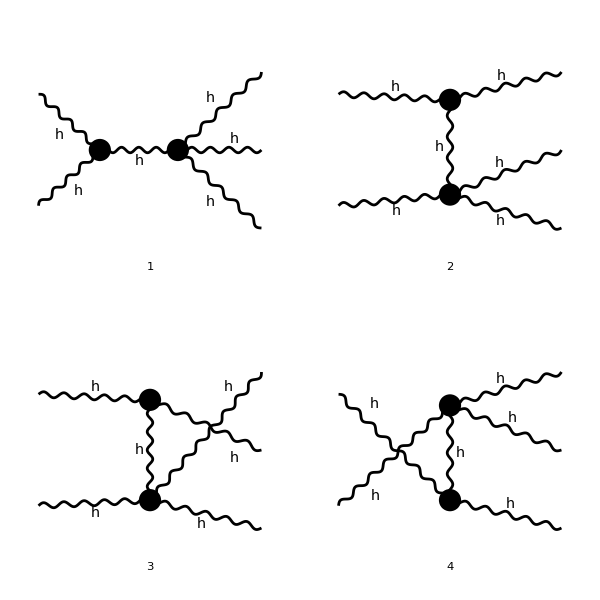

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Five-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->600]
```

```mathematica
If[!TrueQ[fiveGravitonInputsValid[]],Print["AMPLITUDE CONSTRUCTION BLOCKED: the current model, topology set and insertions have not passed the completeness guards, or have changed since they passed."];Print["Re-evaluate this section in order: model guard, topology generation and insertion, insertion guard, then this cell. No amplitude is constructed and no stale insertion or amplitude value is kept."];Clear[fiveGravitonCompleteness,fiveGravitonModelRecord,treeTopologies,treeInsertions,treeRawAmplitude,diagramTensors,externalTensors,theAmplitude5];fiveGravitonInputsValid[]:=False;Abort[]];treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4,p5},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

> Top. 5: 1 Classes amplitude

> Top. 6: 1 Classes amplitude

> Top. 7: 1 Classes amplitude

> Top. 8: 1 Classes amplitude

> Top. 9: 1 Classes amplitude

> Top. 10: 1 Classes amplitude

> Top. 11: 1 Classes amplitude

> Top. 12: 1 Classes amplitude

> Top. 13: 1 Classes amplitude

> Top. 14: 1 Classes amplitude

> Top. 15: 1 Classes amplitude

> Top. 16: 1 Classes amplitude

> Top. 17: 1 Classes amplitude

> Top. 18: 1 Classes amplitude

> Top. 19: 1 Classes amplitude

> Top. 20: 1 Classes amplitude

> Top. 21: 1 Classes amplitude

> Top. 22: 1 Classes amplitude

> Top. 23: 1 Classes amplitude

> Top. 24: 1 Classes amplitude

> Top. 25: 1 Classes amplitude

in total: 25 Classes amplitudes

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ]PolarizationTensorD[p5,μ5,ν5,-ⅈ];
```

```mathematica
theAmplitude5[p1_,p2_,p3_,p4_,p5_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;//Timing
```

```mathematica
Short[theAmplitude5[p1,p2,p3,p4,p5],4]
```

```mathematica
theAmplitude5[p1,p2,p3,p4,p5]//Length
```